2.

3.

-1.77636×10^-15

1.42109×10^-14

6.88005×10^-13

6.80345×10^-13

11

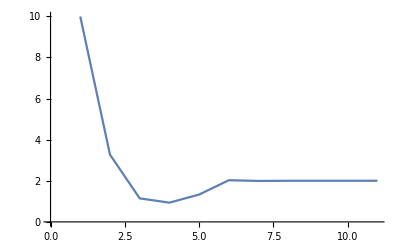

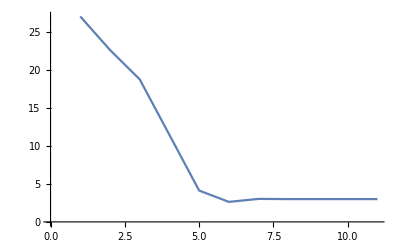

Set::write: Tag And in Errorx && Errory is Protected.

Set::write: Tag And in Errorx && Errory is Protected. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/General/write",
ButtonNote->"Set::write"]

General::stop: Further output of Set :: write will be suppressed during this calculation.

```mathematica
u[x_,y_]=x^2+(x*y)-10;
v[x_,y_]=y+3(x*y^2)-57;
dh=0.001;
Dux[x_,y_]=(u[x+dh,y]-u[x,y])/dh;
Duy[x_,y_]=(u[x,y+dh]-u[x,y])/dh;
Dvx[x_,y_]=(v[x+dh,y]-v[x,y])/dh;
Dvy[x_,y_]=(v[x,y+dh]-v[x,y])/dh;
J[x_,y_]=Dux[x,y]*Dvy[x,y]-Dvx[x,y]*Duy[x,y];
gx[x_,y_]=x-((u[x,y]*Dvy[x,y]-v[x,y]*Duy[x,y])/J[x,y]);
gy[x_,y_]=y-((v[x,y]*Dux[x,y]-u[x,y]*Dvx[x,y])/J[x,y]);
Emin=10^-9;
Nmax=1000;
Iteraciones=0;
Bandera=0;
Errorx=1;
Errory=1;
Datosx={};
Datosy={};

While[((Iteraciones≤10)&&(Bandera==0)&&(Errorx≠0)&&(Errory≠0)),
Xi=Input["Introduce Xi"];
Yi=Input["Introduce Yi"];
If[J[Xi,Yi]≠0,Bandera=1,Bandera=0];
If[u[Xi,Yi]==0&&v[Xi,Yi]==0,(Errorx=0)&&(Errory=0),(Errorx=1)&&(Errory=1)];
Iteraciones++
	]
Iteraciones=0;
While[((Errorx≥ Emin)&&(Errory≥ Emin)&&(Iteraciones≤ Nmax)&&(Bandera==1)),
Xact=gx[Xi,Yi];
AppendTo[Datosx,Xact];
Yact=gy[Xi,Yi];
AppendTo[Datosy,Yact];

If[Xact==0,Xact=Emin, Xact=Xact];
Errorx=Abs[(Xact-Xi)/Xact];
If[Yact==0,Yact=Emin, Yact=Yact];
Errory=Abs[(Yact-Yi)/Yact];
If[u[Xact,Yact]==0&&v[Xact,Yact]==0,(Errorx=0)&&(Errory=0),(Errorx=Errorx)&&(Errory=Errory)];
Xi=Xact;
Yi=Yact;
Iteraciones++
]

Xact//N
Yact//N
u[Xact,Yact]//N
v[Xact,Yact]//N
Errorx//N
Errory//N
Iteraciones
ListPlot[Datosx,Joined->True,PlotRange->All]
ListPlot[Datosy,Joined->True,PlotRange->All]
```